Exercise Q1

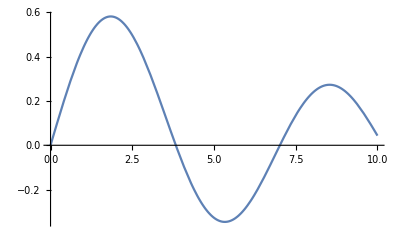

{x→0.}

{x→3.83171}

{x→7.01559}

```mathematica
Plot[BesselJ[1, x], {x, 0, 10}]
FindRoot[BesselJ[1, x], {x, 0}]
FindRoot[BesselJ[1, x], {x, 4}]
FindRoot[BesselJ[1, x], {x, 7}]
```

Exercise Q2

```mathematica
Integrate[Sin[x]* Exp[-x], x]
D[%, x]
Simplify[%]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])

ⅇ^-x Sin[x]

Exercise Q3

```mathematica
Solve[x*Log[x]-3*x+10 == 6, x]
a = N[x/.%[[1]]]
b = N[x/.%%[[2]]]
NSolve[x*Log[x]-3*x+10 == 6, x]
c= x/.%[[1]]
d = x/.%%[[2]]
a-d
b-c
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-4/ProductLog[-4/ⅇ^3]},{x→-4/ProductLog[-1,-4/ⅇ^3]}}

15.5229

1.56883

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1.56883},{x→15.5229}}

1.56883

15.5229

1.77636×10^-15

0.